## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSFittingPackage`"];
Get["MASSFittingPackage`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="GAPD";
KeqEquilibrator=0.408;

(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/MASS_fitting_package/";

mainFolder = "fit_dKd";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder];
```

Working dir:/home/mrama/Dropbox/MASS_fitting_package/examples/

## Import Data

```mathematica
enzymeDataPath = pathData <> "kinetic_data.xls";
bufferInfoDataPath = pathData <> "buffer_info.xls";
ionChargeDataPath = pathData <> "ion_charge.xls";

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
(*Print Available Reaction/Protein Data*)

rxn
mechanism
"Structure "<>ToString@structure
"Active sites "<>ToString@nActiveSites

(*Print Available Kinetic Data*)
{{"Km Values:","(kmList)"},
{"Substrate","Km_Value","CoSubstrate","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~kmList//TableForm
{{"S0.5 Values:","(s05List)"},
{"Substrate","S0.5_Value","CoSubstrate","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~s05List//TableForm
{{"kcat Values:","(kcatList)"},
{"Metabolite(s)","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~kcatList//TableForm
{{"Inhibition Values:","(inhibitionList)"},
{"Parameter_Type","Inhibitor","Value","Inhibition Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~inhibitionList//TableForm
{{"Activation Values:","(activationList)"},
{"Parameter_Type","Activator","Value","Activation Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~activationList//TableForm
{{"Other Parameters:","(otherParms)"},
{"Parameter_Type","Metabolite","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~otherParmsList//TableForm
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi,[nad,g3p,pi,13dpg,nadh]

Structure 4.

Active sites 4.

Km Values: | (kmList) |  |  |  |  |  | 
Substrate | Km_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
nad | 0.000045 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22. | teoa | 0.04 | 
g3p | 0.00089 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22. | teoa | 0.04 | 
pi | 0.00053 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22. | teoa | 0.04 |

S0.5 Values: | (s05List) |  |  |  |  |  | 
Substrate | S0.5_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values: | (kcatList) |  |  |  |  | 
Metabolite(s) | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
g3p | Null
nad | Null
pi | Null | 268. | 1/s | 8.9 | 22. | teoa | 0.04 |

Inhibition Values: | (inhibitionList) |  |  |  |  |  |  | 
Parameter_Type | Inhibitor | Value | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values: | (activationList) |  |  |  |  |  |  | 
Parameter_Type | Activator | Value | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters: | (otherParms) |  |  |  |  |  | 
Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kd | nad | 3.2×10^-7 | M | 8.9 | 22. | teoa | 0.04 |

### Construct enzyme module

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi
"[nad,g3p,pi,1,3-diphosphoglycerate,nadh]"

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&13dpg&nadh",
				"E_GAPD[c]&13dpg&nadh <=> E_GAPD[c]&13dpg + nadh[c]",
				"E_GAPD[c]&13dpg <=> E_GAPD[c] + 13dpg[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

### Setup King-Altmann Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
competitiveRxns={{}};
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getRateConstSubRandomMech[enzymeModel, eqRateConstSub, allCatalyticReactions, nonCatalyticReactions, competitiveRxns];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];

(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

default absoluteFluxEqnRelRateFor

default absoluteFluxEqnRelRateRev

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={8.9, 22};

kmFittingData= simulateKmData[rxn, metsFull, metsSub, metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath, inputPath, fileList, KeqEquilibrator];


kcatFittingData=simulateKcatData[rxn, metsFull, metsSub, metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			  inputPath, fileList, KeqEquilibrator];


haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];


otherParmsList=otherParmsList[[1]];
KdRatio=Subscript[k, GAPD1]^⟵/Subscript[k, GAPD1]^⟶;
KdVal=otherParmsList[[3]];
{KdFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[KdRatio,KdVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, "KdRatio"];


dKdVal =4.25*10^2(*1.92*10^4*);
dKdRatio =(Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵);

{dKdFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[dKdRatio,dKdVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="dKdRatio"];
```

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];
fittingData = Flatten[{kmFittingData,kcatFittingData, KdFittingData,KeqFittingData,dKdFittingData}, 1];

dataPath =inputPath<>rxnName<>".dat";

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath]
```

Keq_GAPD	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_E_total	param_pH	param_Temp	FileFlag	Target_Data
0.408	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.09090909090909098
0.408	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.13680688860321014
0.408	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.20076000891310197
0.408	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.2847472489508014
0.408	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.3868631798468571
0.408	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.5000000000000002
0.408	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.6131368201531433
0.408	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.7152527510491989
0.408	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.7992399910868984
0.408	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.86319311139679
0.408	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt	0.9090909090909093
0.408	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.090909090909091
0.408	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.13680688860321016
0.408	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.20076000891310186
0.408	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.2847472489508016
0.408	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.38686317984685703
0.408	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.5000000000000002
0.408	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.6131368201531434
0.408	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.7152527510491988
0.408	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.7992399910868984
0.408	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.86319311139679
0.408	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt	0.9090909090909092
0.408	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.09090909090909093
0.408	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.13680688860321005
0.408	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.20076000891310172
0.408	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.28474724895080145
0.408	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.3868631798468569
0.408	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.5
0.408	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.6131368201531432
0.408	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.7152527510491988
0.408	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.7992399910868982
0.408	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.8631931113967899
0.408	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt	0.9090909090909092
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0.01	0.01	0	0.01	1	8.9	22.	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt	268.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt	0.408
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.
0.408	0	0	0	0	0	1	8.9	22	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt	425.

## Configure the Particle Swarm Optimization

```mathematica
numTrials=5;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateRev.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateRev_13dpg.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateRev_nadh.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt]
data_file_name	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/GAPD.dat
value_row	-1
function_row	-2
data_row_high	-2
summary_file_name	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/output/raw/summary.txt
ultimate_result_name	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/output/raw/psoResults.txt

## Configure the Levenberg-Marquardt Algorithm

```mathematica
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, lowerParamBound, upperParamBound];
```

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
candidates_import_path	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/output/raw/psoResults.txt
candidates_export_path	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/output/raw/lmaResults.txt
filesWithFunctions	[/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateRev.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateRev_13dpg.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateRev_nadh.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt]
data_file_name	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/GAPD.dat
value_row	-1
function_row	-2
data_row_high	-2

### Make the shell script to run pso and lma fitting methods

```mathematica
runFitScriptPath= pathMASSFittingPackage <> "python_code/src/run_fit_rel.py"
shRunFit=createCombinedFitShellScript[runFitScriptPath, psoParameterPath, lmaParameterPath, psoTrialSummaryFileName, psoResultsFileName, lmaResultsFileName, numTrials, dataPath];

shRunFitPath=inputPath<>"runFit.sh";
Export[shRunFitPath,shRunFit,"Table"];

(*Make the Shell Script Executable*)
mkShRunFitExec="chmod u+x "<> shRunFitPath;
mkShRunFitExecCmd="!"<>mkShRunFitExec<>" 2>&1";
Import[mkShRunFitExecCmd,"Text"];
```

/home/mrama/Dropbox/MASS_fitting_package/python_code/src/run_fit_rel.py

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runBothCmd="cd "<>inputPath<>" && ./"<>"runFit.sh";
runBothExe="!"<>runBothCmd<>" 2>&1";
Import[runBothExe,"Text"]
```

best_fit: 1.07558207756
best_fit: 1.09796373312
best_fit: 2.83472167757
best_fit: 2.80421298275
best_fit: 1.07336240919

#### Run the PSO Algorithm Independently - not working

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"

(*You can copy+paste this output to a shell*)
```

cd /home/mrama/Dropbox/Kinetics/Enzymes_new/GAPD_dKd/Parameter_Fitting/Development/ && ./runPso.sh

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

#### Run the Levenberg-Marquardt Algorithm Independently - not working

The Levenberg-Marquardt Algorithm needs to be run after the Particle Swarm Optimization

```mathematica
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

python /media/users/jdebree/ProjectFiles/Scripts/lma_ver0.10.1.py /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaParameters.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/psoResults.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
lmaRunExe="!"<>lmaRunCmd<>" 2>&1";
Import[lmaRunExe,"Text"]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fittingData = Import[inputPath <> "GAPD.dat"];
fittingData = fittingData[[2;;,All]];
resultsFile = "raw/lmaResults.txt";
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,""];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Relative error | True value | Predicted Value
 |  |  | 
relRateFor_nad | 5.6159×10^-10 | 0.0909091 | 0.0909091
relRateFor_nad | 5.33213×10^-10 | 0.136807 | 0.136807
relRateFor_nad | 4.937×10^-10 | 0.20076 | 0.20076
relRateFor_nad | 4.41832×10^-10 | 0.284747 | 0.284747
relRateFor_nad | 3.78757×10^-10 | 0.386863 | 0.386863
relRateFor_nad | 3.08875×10^-10 | 0.5 | 0.5
relRateFor_nad | 2.3898×10^-10 | 0.613137 | 0.613137
relRateFor_nad | 1.75881×10^-10 | 0.715253 | 0.715253
relRateFor_nad | 1.24005×10^-10 | 0.79924 | 0.79924
relRateFor_nad | 8.45021×10^-11 | 0.863193 | 0.863193
relRateFor_nad | 5.61895×10^-11 | 0.909091 | 0.909091
relRateFor_g3p | 2.49751×10^-9 | 0.0909091 | 0.0909091
relRateFor_g3p | 2.3714×10^-9 | 0.136807 | 0.136807
relRateFor_g3p | 2.1957×10^-9 | 0.20076 | 0.20076
relRateFor_g3p | 1.96497×10^-9 | 0.284747 | 0.284747
relRateFor_g3p | 1.68443×10^-9 | 0.386863 | 0.386863
relRateFor_g3p | 1.37363×10^-9 | 0.5 | 0.5
relRateFor_g3p | 1.06281×10^-9 | 0.613137 | 0.613137
relRateFor_g3p | 7.82252×10^-10 | 0.715253 | 0.715253
relRateFor_g3p | 5.51528×10^-10 | 0.79924 | 0.79924
relRateFor_g3p | 3.75835×10^-10 | 0.863193 | 0.863193
relRateFor_g3p | 2.49745×10^-10 | 0.909091 | 0.909091
relRateFor_pi | 2.58704×10^-9 | 0.0909091 | 0.0909091
relRateFor_pi | 2.45641×10^-9 | 0.136807 | 0.136807
relRateFor_pi | 2.27442×10^-9 | 0.20076 | 0.20076
relRateFor_pi | 2.0354×10^-9 | 0.284747 | 0.284747
relRateFor_pi | 1.74484×10^-9 | 0.386863 | 0.386863
relRateFor_pi | 1.4229×10^-9 | 0.5 | 0.5
relRateFor_pi | 1.10092×10^-9 | 0.613137 | 0.613137
relRateFor_pi | 8.10347×10^-10 | 0.715253 | 0.715253
relRateFor_pi | 5.71336×10^-10 | 0.79924 | 0.79924
relRateFor_pi | 3.89314×10^-10 | 0.863193 | 0.863193
relRateFor_pi | 2.58709×10^-10 | 0.909091 | 0.909091
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
absRateFor | 4.27365×10^-10 | 268. | 268.
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
KdRatio | 5.00543 | 3.2×10^-7 | 3.36017×10^-7
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
haldaneRatio | 6.62936×10^-10 | 0.408 | 0.408
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.
dKdRatio | 7.62237×10^-10 | 425. | 425.

### Simulated Data and Best Fit Data Plot

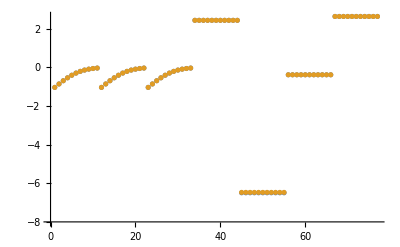

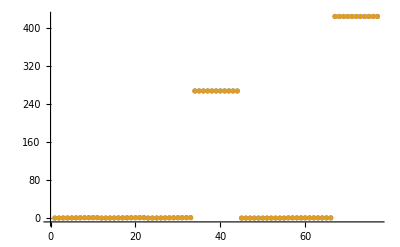

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

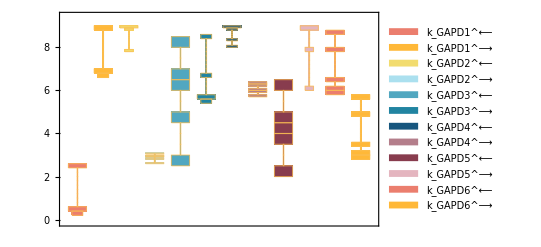

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

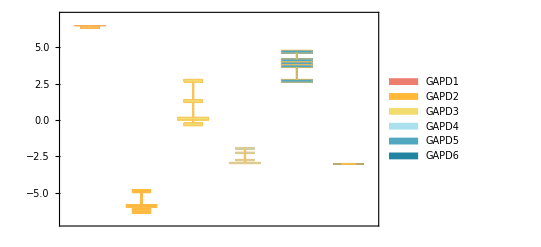

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

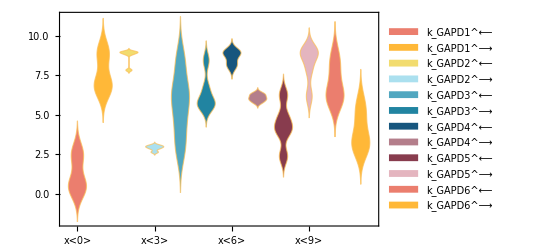

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[inputPath  <> "(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

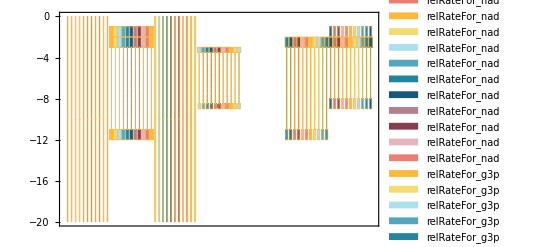

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= Underscript[E_total, Global]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 6.17724×10^-10
0.00089 | 0.00089 | 2.74725×10^-9
0.00053 | 0.00053 | 2.8457×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268. | 268. | 4.27365×10^-10

```mathematica
backCalculateRatios[dKdRatio, dKdVal, paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 7.62237×10^-10